# Relativistic Quantum Mechanics

By: Salazar Ángel and Potosí Quray

## TISE: The Square Well Potential

### 1. Solving the Schrodinger Equation

```mathematica
Subscript[V, 0] :=-2
a := 2
ℏ :=1
m :=1
```

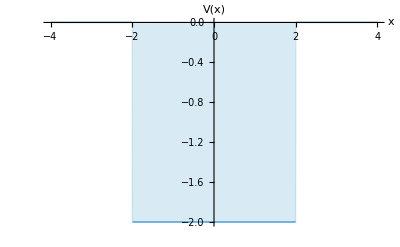

```mathematica
f[x_]:=Piecewise[{{0,x<-a},{Subscript[V,0],-a<=x<=a}}];
Plot[f[x],{x,-4,4},PlotStyle->Thick,AxesLabel->{"x","V(x)"},Filling->Axis]
```

#### Regions to the left and right of the barrier potential

The time-independent Schrodinger Equation has different forms in the regions to the left and right of the barrier potential:

#### First region x<0:

```mathematica
sol1 = DSolve[-ℏ^2/(2 m) Subscript[ψ, 1]''[x] == -En Subscript[ψ, 1][x],Subscript[ψ, 1][x],x];
TrigToExp[sol1]
```

{{ψ_1[x]→ⅇ^(√2 √En x) C[1]+ⅇ^(-√2 √En x) C[2]}}

Let k1 =  (√(-2 m En))/ℏ

```mathematica
Subscript[ψ, 1][x_] :=A Exp[k1 x] +B Exp[ -k1 x] /.{B->0}
```

#### Second Region 0<x>a

```mathematica
sol2= DSolve[-ℏ^2/(2 m) Subscript[ψ, 2]''[x]+V0 Subscript[ψ, 2][x] == -En Subscript[ψ, 2][x],Subscript[ψ, 2][x],x];
TrigToExp[sol2]
```

{{ψ_2[x]→ⅇ^(√2 √(En+V0) x) C[1]+ⅇ^(-√2 √(En+V0) x) C[2]}}

Let k2 =  (√(2 m (En+V0)))/ℏ^2

```mathematica
Subscript[ψ, 2][x_]:=C Exp[I k2 x]+ D Exp[-I k2 x]
```

#### Third Region x>a

```mathematica
sol3=DSolve[-ℏ^2/(2 m) Subscript[ψ, 3]''[x] == -En Subscript[ψ, 3][x],Subscript[ψ, 3][x],x];
TrigToExp[sol3]
```

{{ψ_3[x]→ⅇ^(√2 √En x) C[1]+ⅇ^(-√2 √En x) C[2]}}

```mathematica
Subscript[ψ, 3][x_]:=F Exp[k1 x]+G Exp[- k1 x]/.{F->0}
```

### 2. Getting the system of equations of Boundary Conditions

We apply the matching conditions for ψ(x) and ψ’(x), that is at the points x=-a and x=a, four equations in the arbitrary constants A, B, C, D, and F will be obtained:

```mathematica
eq1 = Subscript[ψ, 1][-a]==Subscript[ψ, 2][-a]
```

A ⅇ^(-2 k1)==C ⅇ^(-2 ⅈ k2)+D ⅇ^(2 ⅈ k2)

```mathematica
eq2 = Subscript[ψ, 2][a] == Subscript[ψ, 3][a]
```

D ⅇ^(-2 ⅈ k2)+C ⅇ^(2 ⅈ k2)==ⅇ^(-2 k1) G

```mathematica
eq3 = Subscript[ψ, 1]'[-a] == Subscript[ψ, 2]'[-a]
```

A ⅇ^(-2 k1) k1==ⅈ C ⅇ^(-2 ⅈ k2) k2-ⅈ D ⅇ^(2 ⅈ k2) k2

```mathematica
eq4 = Subscript[ψ, 2]'[a] == Subscript[ψ, 3]'[a]
```

-ⅈ D ⅇ^(-2 ⅈ k2) k2+ⅈ C ⅇ^(2 ⅈ k2) k2==-ⅇ^(-2 k1) G k1

### 3. Obtaining the Transcendental Equation

We add and subtract equations from the system of equations

```mathematica
eq5 = A Exp[-2 k1]+Exp[-2 k1] G==C Exp[-2 ⅈ k2]+D Exp[2 ⅈ k2]+D Exp[-2 ⅈ k2]+C Exp[2 ⅈ k2]//FullSimplify
```

ⅇ^(-2 k1) (A+G)==2 (C+D) Cos[2 k2]

```mathematica
eq6 = A ⅇ^(-2 k1) k1+ⅇ^(-2 k1) G k1==  ⅈ C ⅇ^(-2 ⅈ k2) k2-ⅈ D ⅇ^(2 ⅈ k2) k2-(-ⅈ D ⅇ^(-2 ⅈ k2) k2+ⅈ C ⅇ^(2 ⅈ k2) k2)//FullSimplify
```

ⅇ^(-2 k1) (A+G) k1==2 (C+D) k2 Sin[2 k2]

```mathematica
eq7 = (ⅇ^(-2 k1) (A+G) k1)/(ⅇ^(-2 k1) (A+G))==(2 (C+D) k2 Sin[2 k2])/(2 (C+D) Cos[2 k2])//FullSimplify
```

k1==k2 Tan[2 k2]

### 4. Finding the roots of the transcendental Equation

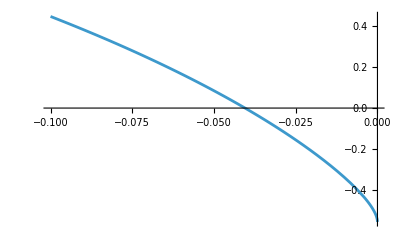

```mathematica
k1[En_?NumericQ]:=√(-2 m En)/ℏ;
k2[En_?NumericQ]:=√(2 m (En+V0))/ℏ;

TrasEq[En_?NumericQ]:=k1[En]-k2[En] Tan[a k2[En]]/.{V0->0.1};
Plot[TrasEq[En],{En,-0.1+10^-6,-10^-6},PlotRange->All]
```

```mathematica
sol=FindRoot[TrasEq[En],{En,-0.02}]
```

{En→-0.0405069}

Now we implement a iterative method to find the roots for a range of values of V0

```mathematica
ClearAll[k1,k2];
k1[En_?NumericQ]:=√(-2 m En)/ℏ;                    (*En<0*)
k2[En_?NumericQ,V0_?NumericQ]:=√(2 m (En-V0))/ℏ; (*En>V0*)

feven[En_?NumericQ,V0_?NumericQ]:=Module[{x},If[!(V0<0&&V0<En<0),Return[Indeterminate]];
x=a k2[En,V0];
If[!FiniteQ[Tan[x]],Return[Indeterminate]];
k1[En]-k2[En,V0] Tan[x]];
```

```mathematica
(*we find one root at a given V0 *)
Clear[EvenEnergyBrent];
EvenEnergyBrent[V0_?NumericQ]:=Module[{pad,emin,emax,grid,vals,seg},If[V0>=0,Return[Missing["NoBoundStates"]]];
pad=Max[1.*^-4,5.*^-3 Abs[V0]];
{emin,emax}={V0+pad,-pad};
grid=Subdivide[emin,emax,600];
vals=Quiet[feven[#,V0]]&/@grid;
seg=SelectFirst[Partition[Transpose[{grid,vals}],2,1],(NumericQ[Times@@Sign[#[[All,2]]]]&&Times@@Sign[#[[All,2]]]<0)&,Missing["NoBracket"]];
If[seg===Missing["NoBracket"],Return[Missing["NoRoot"]]];
En/. FindRoot[feven[En,V0]==0,{En,seg[[1,1]],seg[[2,1]]},Method->"Brent",MaxIterations->300]];

(*Track the lowest even level across a list of V0s,reusing the previous solution as a seed*)
Clear[TrackEvenBranch];
TrackEvenBranch[V0min_:-2.,V0max_:-0.05,dV_:0.05]:=Module[{vlist,pad,lastE=Missing["None"],out={}},vlist=Range[V0min,V0max,dV];
Do[pad=Max[1.*^-4,5.*^-3 Abs[v]];
If[lastE===Missing["None"],lastE=EvenEnergyBrent[v],With[{emin=v+pad,emax=-pad,e0=lastE},lastE=Quiet@Check[En/. FindRoot[feven[En,v]==0,{En,Clip[e0,{emin,emax}]-0.1 Abs[dV],emin,emax},MaxIterations->200],Missing["fail"]];
If[lastE===Missing["fail"],lastE=EvenEnergyBrent[v]];]];
AppendTo[out,{v,lastE}],{v,vlist}];
out];
```

```mathematica
data=TrackEvenBranch[-2.0,-0.05,0.02];
```

### 5. Plot Energy E vs Potential V0

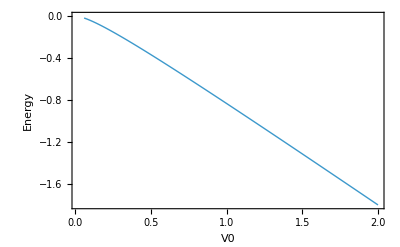

```mathematica
dataPos={-#[[1]],#[[2]]}&/@data;
ListLinePlot[DeleteMissing[dataPos,1,2],Frame->True,PlotRange->All,PlotStyle->Thick,FrameLabel->{"V0","Energy"}]
```

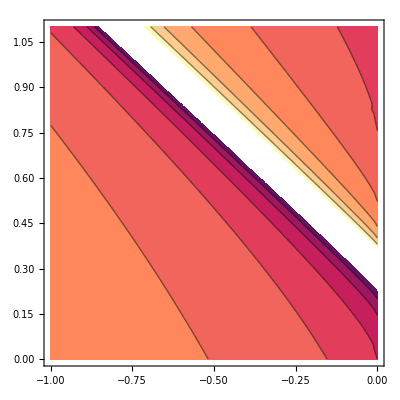

```mathematica
ContourPlot[k1[En]-k2[En,-V0] Tan[k2[En,-V0] a],{En,-1,0},{V0,0,1.1}]
```

### 6. Table

```mathematica
dataPosHeader=dataPos;
tableWithHeader=Prepend[dataPos,{"V0 ","E"}]//TableForm
```

V0  | E
2. | -1.80395
1.98 | -1.78436
1.96 | -1.76478
1.94 | -1.7452
1.92 | -1.72563
1.9 | -1.70606
1.88 | -1.6865
1.86 | -1.66694
1.84 | -1.64739
1.82 | -1.62784
1.8 | -1.60831
1.78 | -1.58877
1.76 | -1.56925
1.74 | -1.54973
1.72 | -1.53021
1.7 | -1.51071
1.68 | -1.49121
1.66 | -1.47172
1.64 | -1.45223
1.62 | -1.43276
1.6 | -1.41329
1.58 | -1.39383
1.56 | -1.37437
1.54 | -1.35493
1.52 | -1.33549
1.5 | -1.31607
1.48 | -1.29665
1.46 | -1.27724
1.44 | -1.25784
1.42 | -1.23845
1.4 | -1.21908
1.38 | -1.19971
1.36 | -1.18035
1.34 | -1.16101
1.32 | -1.14167
1.3 | -1.12235
1.28 | -1.10304
1.26 | -1.08374
1.24 | -1.06446
1.22 | -1.04519
1.2 | -1.02593
1.18 | -1.00669
1.16 | -0.987462
1.14 | -0.96825
1.12 | -0.949055
1.1 | -0.929876
1.08 | -0.910715
1.06 | -0.891571
1.04 | -0.872446
1.02 | -0.853341
1. | -0.834256
0.98 | -0.815191
0.96 | -0.796149
0.94 | -0.777129
0.92 | -0.758133
0.9 | -0.739162
0.88 | -0.720217
0.86 | -0.701298
0.84 | -0.682408
0.82 | -0.663548
0.8 | -0.644719
0.78 | -0.625922
0.76 | -0.60716
0.74 | -0.588433
0.72 | -0.569745
0.7 | -0.551097
0.68 | -0.532491
0.66 | -0.51393
0.64 | -0.495416
0.62 | -0.476952
0.6 | -0.458542
0.58 | -0.440188
0.56 | -0.421895
0.54 | -0.403666
0.52 | -0.385507
0.5 | -0.367422
0.48 | -0.349416
0.46 | -0.331497
0.44 | -0.31367
0.42 | -0.295944
0.4 | -0.278327
0.38 | -0.26083
0.36 | -0.243463
0.34 | -0.226239
0.32 | -0.209174
0.3 | -0.192285
0.28 | -0.175593
0.26 | -0.15912
0.24 | -0.142895
0.22 | -0.126954
0.2 | -0.111337
0.18 | -0.0960957
0.16 | -0.0812956
0.14 | -0.067019
0.12 | -0.0533744
0.1 | -0.0405069
0.08 | -0.0286184
0.06 | -0.0180006